```mathematica
DateString[]
$Version
```

Sun 22 Sep 2019 16:19:54

12.0.0 for Microsoft Windows (64-bit) (April 6, 2019)

## Lecture 05 edited by Chi-Ok Hwang, originally made by Dr. 전 경원

[1] S. Wolfram, An Elementary Introduction to the Wolfram Language, 2nd ed. Wolfram Media, Inc., 2017.

-Graphics-

### 25 Ways to Apply Functions

25 Ways to Apply Functions

When you write f[x] it means “apply the function f to x”. An alternative way to write the same thing in the Wolfram Language is f@x.

```mathematica
f@x
```

f[x]

```mathematica
f@g@h@x
```

f[g[h[x]]]

There’s a third way to write f[x] in the Wolfram Language:as an “afterthought”,in the form x//f.

```mathematica
x//f
```

f[x]

```mathematica
x//f//g//h
```

h[g[f[x]]]

```mathematica
2 Pi^3+1//N
```

63.0126

In working with the Wolfram Language, a powerful notation that one ends up using all the time is /@, which means “apply to each element”.

```mathematica
f/@{1,2,3}
```

{f[1],f[2],f[3]}

```mathematica
Map[f,{1,2,3}]
```

{f[1],f[2],f[3]}

```mathematica
Hue/@{0.1,0.2,0.3,0.4}
```

{Hue[0.1],Hue[0.2],Hue[0.3],Hue[0.4]}

```mathematica
{Hue[0.1],Hue[0.2],Hue[0.3],Hue[0.4]}
```

{Hue[0.1],Hue[0.2],Hue[0.3],Hue[0.4]}

```mathematica
Range/@{3,2,5,6,7}
```

{{1,2,3},{1,2},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7}}

```mathematica
{Range[3],Range[2],Range[5],Range[6],Range[7]}
```

{{1,2,3},{1,2},{1,2,3,4,5},{1,2,3,4,5,6},{1,2,3,4,5,6,7}}

Some calculational functions are listable, which means they automatically apply themselves to elements in a list.

```mathematica
N[{1/3,1/4,1/5,1/6}]
```

{0.333333,0.25,0.2,0.166667}

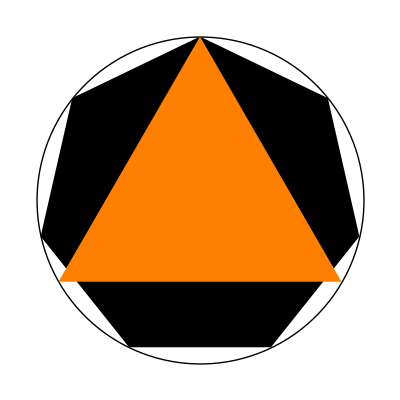

```mathematica
Graphics[{Circle[],RegularPolygon[7],Style[RegularPolygon[3],Orange]}]
```


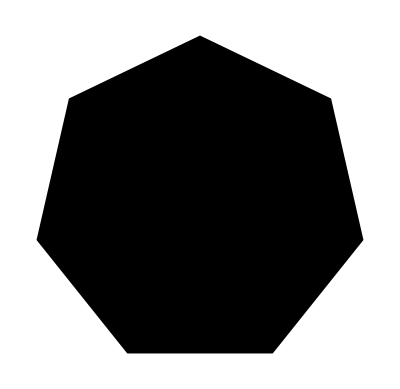
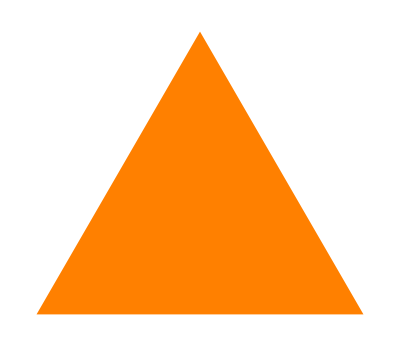

```mathematica
Graphics/@{Circle[],RegularPolygon[7],Style[RegularPolygon[3],Orange]}
```

Picky exercises: 4, 7

Tweet-a-Program:

```mathematica
Row[Style[#,5#+1]&/@First[RealDigits[π,10,1000]]]
```

3141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117067982148086513282306647093844609550582231725359408128481117450284102701938521105559644622948954930381964428810975665933446128475648233786783165271201909145648566923460348610454326648213393607260249141273724587006606315588174881520920962829254091715364367892590360011330530548820466521384146951941511609433057270365759591953092186117381932611793105118548074462379962749567351885752724891227938183011949129833673362440656643086021394946395224737190702179860943702770539217176293176752384674818467669405132000568127145263560827785771342757789609173637178721468440901224953430146549585371050792279689258923542019956112129021960864034418159813629774771309960518707211349999998372978049951059731732816096318595024459455346908302642522308253344685035261931188171010003137838752886587533208381420617177669147303598253490428755468731159562863882353787593751957781857780532171226806613001927876611195909216420198

### 26.0 Pure Functions

```mathematica
The advantage of a pure function is that it does not require a separate definition or a name:
Function[x,body]	a pure function in which x is replaced by any argument you provide
     Function[{x1,x2,…},body]	a pure function that takes several arguments
      body&	a pure function in which arguments are specified as # or #1, #2, #3, etc.
```

#### Map?

```mathematica
f=Function[{x,y},x+y]
```

Function[{x,y},x+y]

```mathematica
f[3,4]
```

7

```mathematica
g=(#1+#2)&
```

#1+#2&

```mathematica
g[3,4]
```

7

```mathematica
(#1+#2)&[3,4]
```

7

```mathematica
h[x_]:=f[x]+g[x]
Map[h,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
Map[h,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

```mathematica
Map[f[#]+g[#]&,{a,b,c}]
```

{f[a]+g[a],f[b]+g[b],f[c]+g[c]}

#^2& is a short form for a pure function that squares its argument.

```mathematica
Map[#^2&,a b c]
Map[#^2&,a+b+c]
```

a^2 b^2 c^2

a^2+b^2+c^2

```mathematica
Map[Take[#,2]&,{{2,1,7},{4,1,5},{3,1,2}}]
```

{{2,1},{4,1},{3,1}}

### 26 Pure Anonymous Functions

26 Pure Anonymous Functions

After all the examples we’ve seen of the Wolfram Language, we’re now ready to go to a slightly higher level of abstraction, and tackle the very important concept of pure functions (also known as pure anonymous functions). Using pure functions will let us unlock a new level of power in the Wolfram Language, and also let us redo some of the things we’ve done before in a simpler and more elegant way.

Picky exercises: 5, 8

Tweet-a-Program:

```mathematica
Range[5]
```

{1,2,3,4,5}

```mathematica
Tuples[Range[5],3]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5}}

```mathematica
Graphics3D[{Yellow,Cuboid[{0,0,0}],Blue,Cuboid[{0.5,0.5,0.5}]}]
```

-Graphics3D-

```mathematica
Graphics3D[{RGBColor[#/5],Opacity[.8],Cuboid[#,#+.8]}&/@Tuples[Range[5],3]]
```

-Graphics3D-

### 27 Applying Functions Repeatedly

27 Applying Functions Repeatedly

Picky exercises: 1, 5, 8, 9, 11, +2

```mathematica
NestList[f,x,4]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]]}

```mathematica
Framed[1/x+y]
```

1/x+y

```mathematica
NestList[Framed,x,5]
```

{x,x,x,x,x,x}

```mathematica
NestList[Subsuperscript[#,#,#]&,o,6]
```

{o,o_o^o,(o_o^o)_(o_o^o)^(o_o^o),((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)),(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))),((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))_((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))^((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))),(((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))_((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))^((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))))_(((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))_((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))^((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))))^(((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))_((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o))))^((((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))_(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))^(((o_o^o)_(o_o^o)^(o_o^o))_((o_o^o)_(o_o^o)^(o_o^o))^((o_o^o)_(o_o^o)^(o_o^o)))))}

From Wolfram Community: 
Tutorials links for building a Web Crawler?

```mathematica
NestGraph[Import[#,"Hyperlinks"]&,"http://www.google.com",2,VertexLabels->Placed["Name",Tooltip],GraphStyle->"LargeNetwork",DirectedEdges->False]
```

-Graphics-

### 28 Tests and Conditionals

28 Tests and Conditionals

Testing statements including equality

```mathematica
2+2==4
```

True

```mathematica
2*2>5
```

False

```mathematica
If[2+2==4,x,y]
If[#<4,x,y]&/@{1,2,3,4,5,6,7}
ImageInstanceQ[-Graphics-, Entity["Species", "Species:FelisCatus"]]

Select[{-Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-, -Graphics-},  ImageInstanceQ[#, Entity["Species", "Species:FelisCatus"]] &]
```

x

{x,x,x,y,y,y,y}

$Aborted

{-Graphics-}

Picky exercises: 3, 5, 6, 9, 10, 11, 12, +4, +6